

```mathematica
Plot[x,{x,-2,2}]
```

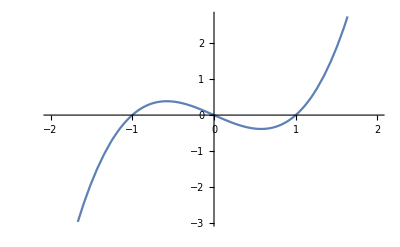

```mathematica
Plot[x^3-x,{x,-2,2}]
```

```mathematica
FullSimplify[Abs[D[x^3-x,{x,2}]/((√(1+D[x^3-x,x]^2))^3)],x∈Reals]
```

(6 Abs[x])/((1+(1-3 x^2)^2)^(3/2))

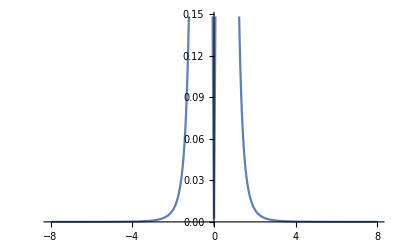

```mathematica
Plot[(6 Abs[x])/((1+(1-3 x^2)^2)^(3/2)),{x,-8,8}]
```

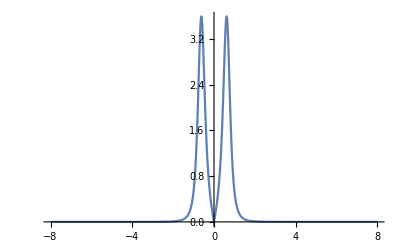

```mathematica
Plot[(6 Abs[x])/((1+(1-3 x^2)^2)^(3/2)),{x,-8,8},PlotRange->Full]
```

```mathematica
Limit[Integrate[(6 Abs[x])/((1+(1-3 x^2)^2)^(3/2)),{x,0,a}],a->∞]
```

$Aborted

```mathematica
Limit[NIntegrate[(6 Abs[x])/((1+(1-3 x^2)^2)^(3/2)),{x,0,a}],a->∞]
```

NIntegrate::nlim: x = a is not a valid limit of integration.

$Aborted

```mathematica
Manipulate[
NIntegrate[(6 Abs[x])/((1+(1-3 x^2)^2)^(3/2)),{x,0,a}]
,{a,.01,1000}]
```

```mathematica
Manipulate[
2NIntegrate[(6 Abs[x])/((1+(1-3 x^2)^2)^(3/2)),{x,0,a}]
,{a,.01,1000}]
```

```mathematica
{x,x^3-x}+Normalize@{1,3 x^2-1}
```

{x+1/(√(1+Abs[-1+3 x^2]^2)),-x+x^3+(-1+3 x^2)/(√(1+Abs[-1+3 x^2]^2))}

```mathematica
FullSimplify[{x,x^3-x}+Normalize@{1,3 x^2-1},x∈Reals]
```

{x+1/(√(1+(1-3 x^2)^2)),-x+x^3+(-1+3 x^2)/(√(1+(1-3 x^2)^2))}

```mathematica
FullSimplify[{x,x^3-x}+ α Normalize@{1,3 x^2-1},x∈Reals]
```

{x+α/(√(1+(1-3 x^2)^2)),-x+x^3+((-1+3 x^2) α)/(√(1+(1-3 x^2)^2))}

```mathematica
FullSimplify[{x,x^3-x}+ α Normalize@{1,3 x^2-1},{α,x}∈Reals]
```

{x+α/(√(1+(1-3 x^2)^2)),-x+x^3+((-1+3 x^2) α)/(√(1+(1-3 x^2)^2))}

```mathematica
Manipulate[
ParametricPlot[
{x+α/(√(1+(1-3 x^2)^2)),-x+x^3+((-1+3 x^2) α)/(√(1+(1-3 x^2)^2))}
,{x,-2,2}]
,{α,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{x+α,-(x+α)+(x+α)^3}
,{x,-2,2}]
,{α,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{x+α,-(x+(3 α^2+1))+(x+((3 α^2+1)))^3}
,{x,-2,2}]
,{α,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{x+α,-(x+(3 α^2+1))+(x+((3 α^2+1)))^3}
,{x,-2,2}]
,{α,-1,1}]
```

```mathematica
D[x^3-x,x]/.x->0
```

-1

```mathematica
FullSimplify[Normalize@D[{x,x^3-x},x],x∈Reals]
```

{1/(√(1+(1-3 x^2)^2)),(-1+3 x^2)/(√(1+(1-3 x^2)^2))}

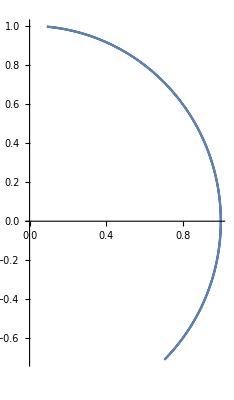

```mathematica
ParametricPlot[
{1/(√(1+(1-3 x^2)^2)),(-1+3 x^2)/(√(1+(1-3 x^2)^2))}
,{x,-2,2}]
```

```mathematica
Integrate[{1/(√(1+(1-3 x^2)^2)),(-1+3 x^2)/(√(1+(1-3 x^2)^2))},x]
```

{-((-1-ⅈ)^(3/2) √(2-(3+3 ⅈ) x^2) √(2-(3-3 ⅈ) x^2) EllipticF[ⅈ ArcSinh[√(-3/2-(3 ⅈ)/2) x],-ⅈ])/(2 √6 √(2-6 x^2+9 x^4)),((-1-ⅈ)^(3/2) √(2-(3+3 ⅈ) x^2) √(2-(3-3 ⅈ) x^2) ((1+ⅈ) EllipticE[ⅈ ArcSinh[√(-3/2-(3 ⅈ)/2) x],-ⅈ]-ⅈ EllipticF[ⅈ ArcSinh[√(-3/2-(3 ⅈ)/2) x],-ⅈ]))/(2 √6 √(2-6 x^2+9 x^4))}

```mathematica
ComplexPlot[
((-1-ⅈ)^(3/2) √(2-(3+3 ⅈ) x^2) √(2-(3-3 ⅈ) x^2) ((1+ⅈ) EllipticE[ⅈ ArcSinh[√(-3/2-(3 ⅈ)/2) x],-ⅈ]-ⅈ EllipticF[ⅈ ArcSinh[√(-3/2-(3 ⅈ)/2) x],-ⅈ]))/(2 √6 √(2-6 x^2+9 x^4))
,{x,-5-5I,5+5I}]
```

-Graphics-

```mathematica
{x,x^3-x}+α{1/(√(1+(1-3 x^2)^2)),(-1+3 x^2)/(√(1+(1-3 x^2)^2))}
```

{x+α/(√(1+(1-3 x^2)^2)),-x+x^3+((-1+3 x^2) α)/(√(1+(1-3 x^2)^2))}

```mathematica
FullSimplify[{x,x^3-x}+α{1/(√(1+(1-3 x^2)^2)),(-1+3 x^2)/(√(1+(1-3 x^2)^2))},{x,α}∈Reals]
```

{x+α/(√(1+(1-3 x^2)^2)),-x+x^3+((-1+3 x^2) α)/(√(1+(1-3 x^2)^2))}

```mathematica
Manipulate[
ParametricPlot[
{x+α/(√(1+(1-3 x^2)^2)),-x+x^3+((-1+3 x^2) α)/(√(1+(1-3 x^2)^2))}
,{x,-2,2}]
,{α,.1,5}]
```

```mathematica
Manipulate[
ParametricPlot[
{x+α/(√(1+(1-3 x^2)^2)),-x+x^3+((-1+3 x^2) α)/(√(1+(1-3 x^2)^2))}
,{x,-2,2}]
,{α,-10,10}]
```

```mathematica
Manipulate[
ParametricPlot[
{x+α/(√(1+(1-3 0^2)^2)),-x+x^3+((-1+3 0^2) α)/(√(1+(1-3 0^2)^2))}
,{x,-2,2}]
,{α,-10,10}]
```

```mathematica
Manipulate[
ParametricPlot[
{x+α/(√(1+(1-3 0^2)^2)),-(x+α)+(x+α)^3+((-1+3 0^2) α)/(√(1+(1-3 0^2)^2))}
,{x,-2,2}]
,{α,-10,10}]
```

```mathematica
Plot[x^3-x,{x,-2,2}]
```

-Graphics-

```mathematica
Manipulate[
Plot[α x^3-x,{x,-2,2},PlotRange->{-2,2}]
,{{α,0},-5,5}]
```

```mathematica
x^3
```

x^3

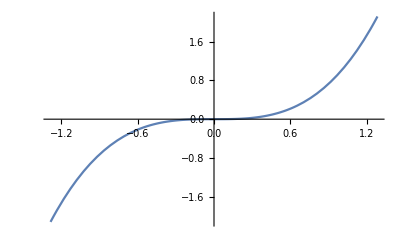

```mathematica
Plot[x^3,{x,-1.2851194708927707,1.2851194708927707}]
```

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
{x,x^3}.RotationMatrix[ⅇ^(-x^2/2)π]
```

{x Cos[ⅇ^(-x^2/2) π]+x^3 Sin[ⅇ^(-x^2/2) π],x^3 Cos[ⅇ^(-x^2/2) π]-x Sin[ⅇ^(-x^2/2) π]}

```mathematica
FullSimplify[{x Cos[ⅇ^(-x^2/2) π]+x^3 Sin[ⅇ^(-x^2/2) π],x^3 Cos[ⅇ^(-x^2/2) π]-x Sin[ⅇ^(-x^2/2) π]},x∈Reals]
```

{x (Cos[ⅇ^(-x^2/2) π]+x^2 Sin[ⅇ^(-x^2/2) π]),x^3 Cos[ⅇ^(-x^2/2) π]-x Sin[ⅇ^(-x^2/2) π]}

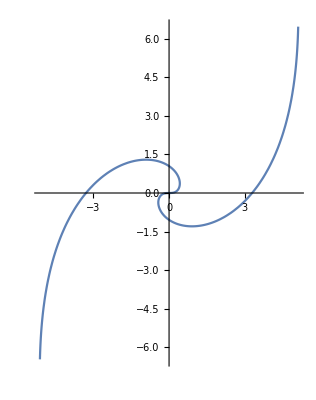

```mathematica
ParametricPlot[
{x (Cos[ⅇ^(-x^2/2) π]+x^2 Sin[ⅇ^(-x^2/2) π]),x^3 Cos[ⅇ^(-x^2/2) π]-x Sin[ⅇ^(-x^2/2) π]}
,{x,-2,2}]
```

```mathematica
Manipulate[
ParametricPlot[
{x (Cos[ⅇ^(-x^2/2) π]+x^2 Sin[ⅇ^(-x^2/2) π]),x^3 Cos[ⅇ^(-x^2/2) π]-x Sin[ⅇ^(-x^2/2) θ]}
,{x,-2,2}]
,{θ,0,2π,π/8}]
```

```mathematica
Manipulate[
ParametricPlot[
{x (Cos[ⅇ^(-x^2/2) π]+x^2 Sin[ⅇ^(-x^2/2) π]),x^3 Cos[ⅇ^(-x^2/2) π]-x Sin[ⅇ^(-x^2/2) θ]}
,{x,-2,2},PlotRange->{-2,2}]
,{θ,0,2π,π/8}]
```

```mathematica
Manipulate[
ParametricPlot[
{x (Cos[ⅇ^(-x^2/2) θ]+x^2 Sin[ⅇ^(-x^2/2) θ]),x^3 Cos[ⅇ^(-x^2/2) θ]-x Sin[ⅇ^(-x^2/2) θ]}
,{x,-2,2},PlotRange->{-2,2}]
,{θ,0,2π,π/8}]
```

```mathematica
Manipulate[
ParametricPlot[
{x (Cos[ⅇ^(-x^2/2) θ]+x^2 Sin[ⅇ^(-x^2/2) θ]),x^3 Cos[ⅇ^(-x^2/2) θ]-x Sin[ⅇ^(-x^2/2) θ]}
,{x,-4,4},PlotRange->{-4,4}]
,{θ,0,2π,π/8}]
```

```mathematica
{x,x}+D[{x,x},x]
```

{1+x,1+x}

```mathematica
FullSimplify[{x,x}+Normalize@D[{x,x},x],x∈Reals]
```

{1/(√2)+x,1/(√2)+x}

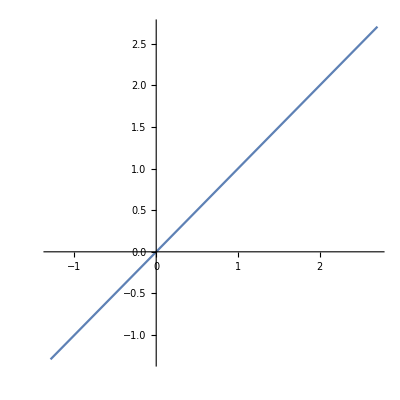

```mathematica
ParametricPlot[
{1/(√2)+x,1/(√2)+x}
,{x,-2,2}]
```

```mathematica
FullSimplify[{x,x}+α Normalize@D[{x,x},x],{x,α}∈Reals]
```

{x+α/(√2),x+α/(√2)}

```mathematica
Manipulate[
ParametricPlot[
{x+α/(√2),x+α/(√2)},{x,-2,2}]
,{α,0,5}]
```

```mathematica
With[{f=Function[x,x]},
Manipulate[
ParametricPlot[
{x,f[x]}+α FullSimplify[Normalize@D[{x,f[x]},x],Element[x,Reals]]
,{x,-2,2}]
,{α,0,5}]
]
```

General::ivar: -1.99992 is not a valid variable.

General::ivar: -1.91829 is not a valid variable.

General::ivar: -1.83665 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
With[{f=Function[x,x]},
Manipulate[
ParametricPlot[
{x,f[x]}+α Normalize@D[{x,f[x]},x]
,{x,-2,2}]
,{α,0,5}]
]
```

General::ivar: -1.99992 is not a valid variable.

```mathematica
With[{f=Function[x,x]},
With[{g={x,f[x]}+α FullSimplify[Normalize@D[{x,f[x]},x],Element[x,Reals]]},
Manipulate[
ParametricPlot[
g
,{x,-2,2}]
,{α,0,5}]
]]
```

```mathematica
With[{f=Function[x,x^2]},
With[{g={x,f[x]}+α FullSimplify[Normalize@D[{x,f[x]},x],Element[x,Reals]]},
Manipulate[
ParametricPlot[
g
,{x,-2,2}]
,{α,0,5}]
]]
```

```mathematica
f[x+α]==f[x]+∫_x^(x+α) f'[t]ⅆt
```

f[x+α]==f[x]+∫_x^(x+α) f'[t]ⅆt

```mathematica
f[x+α]==f[x]+∫_x^(x+α) f'[t]ⅆt
```

f[x+α]==f[x]+∫_x^(x+α) f'[t]ⅆt

```mathematica
FindInstance[f[x+α]==f[x]+∫_x^(x+α) f'[t]ⅆt,{t,x,α}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[f[x+α]==f[x]+∫_x^(x+α) f'[t]ⅆt,{t,x,α}]

```mathematica
FullSimplify[{x,x^2}+Normalize@D[{x,x^2},x],x∈Reals]
```

{x+1/(√(1+4 x^2)),x (x+2/(√(1+4 x^2)))}

```mathematica
(1+Cos[π θ])/2==f''[θ]/((√(1+f'[θ]^2))^3)
```

1/2 (1+Cos[π θ])==f''[θ]/((1+f'[θ]^2)^(3/2))

```mathematica
DSolve[1/2 (1+Cos[π θ])==f''[θ]/((1+f'[θ]^2)^(3/2)),{f[θ],f[θ]},{θ}]
```

{{f[θ]→C[2]+-(ⅈ (2 π C[1]+π K[1]+Sin[π K[1]]))/(√(-4 π^2+4 π^2 C[1]^2+4 π^2 C[1] K[1]+π^2 K[1]^2+4 π C[1] Sin[π K[1]]+2 π K[1] Sin[π K[1]]+Sin[π K[1]]^2))K[1]1θ},{f[θ]→C[2]+(ⅈ (2 π C[1]+π K[2]+Sin[π K[2]]))/(√(-4 π^2+4 π^2 C[1]^2+4 π^2 C[1] K[2]+π^2 K[2]^2+4 π C[1] Sin[π K[2]]+2 π K[2] Sin[π K[2]]+Sin[π K[2]]^2))K[2]1θ}}

```mathematica
-(ⅈ (2 π C[1]+π K[1]+Sin[π K[1]]))/(√(-4 π^2+4 π^2 C[1]^2+4 π^2 C[1] K[1]+π^2 K[1]^2+4 π C[1] Sin[π K[1]]+2 π K[1] Sin[π K[1]]+Sin[π K[1]]^2))K[1]1θ/.K[1]->θ
```

-(ⅈ (π θ+2 π C[1]+Sin[π θ]))/(√(-4 π^2+π^2 θ^2+4 π^2 θ C[1]+4 π^2 C[1]^2+2 π θ Sin[π θ]+4 π C[1] Sin[π θ]+Sin[π θ]^2))θ1θ

```mathematica
-(ⅈ (2 π C[1]+π K[1]+Sin[π K[1]]))/(√(-4 π^2+4 π^2 C[1]^2+4 π^2 C[1] K[1]+π^2 K[1]^2+4 π C[1] Sin[π K[1]]+2 π K[1] Sin[π K[1]]+Sin[π K[1]]^2))K[1]1θ/.K[1]->x
```

-(ⅈ (π x+2 π C[1]+Sin[π x]))/(√(-4 π^2+π^2 x^2+4 π^2 x C[1]+4 π^2 C[1]^2+2 π x Sin[π x]+4 π C[1] Sin[π x]+Sin[π x]^2))x1θ

```mathematica
-(ⅈ (π x+2 π C[1]+Sin[π x]))/(√(-4 π^2+π^2 x^2+4 π^2 x C[1]+4 π^2 C[1]^2+2 π x Sin[π x]+4 π C[1] Sin[π x]+Sin[π x]^2))x1θ/.C[1]->1
```

-(ⅈ (2 π+π x+Sin[π x]))/(√(4 π^2 x+π^2 x^2+4 π Sin[π x]+2 π x Sin[π x]+Sin[π x]^2))x1θ

```mathematica
ⅈ Activate[-(2 π+π x+Sin[π x])/(√(4 π^2 x+π^2 x^2+4 π Sin[π x]+2 π x Sin[π x]+Sin[π x]^2))x1θ]
```

ⅈ ∫_1^θ -(2 π+π x+Sin[π x])/(√(4 π^2 x+π^2 x^2+4 π Sin[π x]+2 π x Sin[π x]+Sin[π x]^2))ⅆx

```mathematica
FullSimplify[ⅈ ∫_1^θ -(2 π+π x+Sin[π x])/(√(4 π^2 x+π^2 x^2+4 π Sin[π x]+2 π x Sin[π x]+Sin[π x]^2))ⅆx]
```

$Aborted

```mathematica
{x,x}+α Normalize[D[{x,x},x]]
```

{x+α/(√2),x+α/(√2)}

```mathematica
{x[t],y[t]}+α Normalize[D[{x[t],y[t]},t]]
```

{x[t]+(α x'[t])/(√(Abs[x'[t]]^2+Abs[y'[t]]^2)),y[t]+(α y'[t])/(√(Abs[x'[t]]^2+Abs[y'[t]]^2))}

```mathematica
FullSimplify[{x[t]+(α x'[t])/(√(Abs[x'[t]]^2+Abs[y'[t]]^2)),y[t]+(α y'[t])/(√(Abs[x'[t]]^2+Abs[y'[t]]^2))},{t,α,x[t],x'[t],y[t],y'[t]}∈Reals]
```

{x[t]+(α x'[t])/(√(x'[t]^2+y'[t]^2)),y[t]+(α y'[t])/(√(x'[t]^2+y'[t]^2))}

```mathematica
{x[t]+(α x'[t])/(√(x'[t]^2+y'[t]^2)),y[t]+(α y'[t])/(√(x'[t]^2+y'[t]^2))}/.{x[t]->x,x'[t]->1}
```

{x+α/(√(1+y'[t]^2)),y[t]+(α y'[t])/(√(1+y'[t]^2))}

```mathematica
{x[t]+(α x'[t])/(√(x'[t]^2+y'[t]^2)),y[t]+(α y'[t])/(√(x'[t]^2+y'[t]^2))}/.{x[t]->x,x'[t]->1,y[t]->y[x],y'[t]->y'[t]}
```

{x+α/(√(1+y'[t]^2)),y[x]+(α y'[t])/(√(1+y'[t]^2))}

```mathematica
{x[t]+(α x'[t])/(√(x'[t]^2+y'[t]^2)),y[t]+(α y'[t])/(√(x'[t]^2+y'[t]^2))}/.{x[t]->x,x'[t]->1,y[t]->y[x],y'[t]->y'[x]}
```

{x+α/(√(1+y'[x]^2)),y[x]+(α y'[x])/(√(1+y'[x]^2))}

```mathematica
{x+α/(√(1+y'[x]^2)),y[x]+(α y'[x])/(√(1+y'[x]^2))}/.y[x]->x^2
```

{x+α/(√(1+y'[x]^2)),x^2+(α y'[x])/(√(1+y'[x]^2))}

```mathematica
{x+α/(√(1+y'[x]^2)),y[x]+(α y'[x])/(√(1+y'[x]^2))}/.y'[x]->2x
```

{x+α/(√(1+4 x^2)),(2 x α)/(√(1+4 x^2))+y[x]}

```mathematica
{x+α/(√(1+y'[x]^2)),y[x]+(α y'[x])/(√(1+y'[x]^2))}/.{y[x]->x^2,y'[x]->2x}
```

{x+α/(√(1+4 x^2)),x^2+(2 x α)/(√(1+4 x^2))}

```mathematica
{x+α/(√(1+4 x^2)),(x+(2 x α)/(√(1+4 x^2)))^2}
```

{x+α/(√(1+4 x^2)),(x+(2 x α)/(√(1+4 x^2)))^2}

```mathematica
Manipulate[
ParametricPlot[
{x+α/(√(1+4 x^2)),(x+(2 x α)/(√(1+4 x^2)))^2}
,{x,-2,2}]
,{α,0,1}]
```

```mathematica
{x+α,(x+∫_0^α √(1+4 x^2)ⅆx)^2}
```

{x+α,ConditionalExpression[(x+1/4 (2 α √(1+4 α^2)+ArcSinh[2 α]))^2,Re[α]≠0||-1/2<Im[α]<0||0<Im[α]<1/2]}

```mathematica
FullSimplify[{x+α,(x+∫_0^α √(1+4 x^2)ⅆx)^2},{x,α}∈Reals]
```

{x+α,ConditionalExpression[(x+1/4 (2 α √(1+4 α^2)+ArcSinh[2 α]))^2,α≠0]}

```mathematica
FullSimplify[{x+α,(x+∫_0^α √(1+4 x^2)ⅆx)^2},x∈Reals∧α∈]
```

{x+α,(x+1/4 (2 α √(1+4 α^2)+ArcSinh[2 α]))^2}

```mathematica
Manipulate[
ParametricPlot[
{x+α,(x+1/4 (2 α √(1+4 α^2)+ArcSinh[2 α]))^2}
,{x,-2,2}]
,{α,0.1,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{x+α,(x+α)^2}
,{x,-2,2}]
,{α,0.1,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{x-α,(x-α)^2}
,{x,-2,2}]
,{α,0.1,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{x-α,(x-α)^2}
,{x,-2,2}]
,{α,0.1,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{x-α,(x-α(2x))^2}
,{x,-2,2}]
,{α,0.1,1}]
```

```mathematica
Solve[1==∫_0^α √(1+4 x^2)ⅆx,α,]
```

{{α→Root0.764Root[{-4+Log[2 #1+√(1+4 #1^2)]+2 #1 √(1+4 #1^2)&,0.76392666331709104116}]0.763926663317091}}

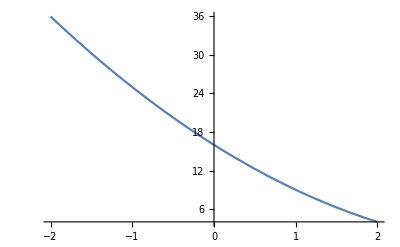

```mathematica
Plot[(x-4)^2,{x,-2,2}]
```

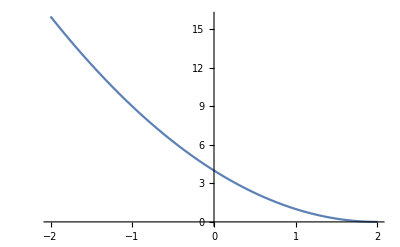

```mathematica
Plot[(x-2)^2,{x,-2,2}]
```



```mathematica
Plot[x^2,{x,-2,2}]
```

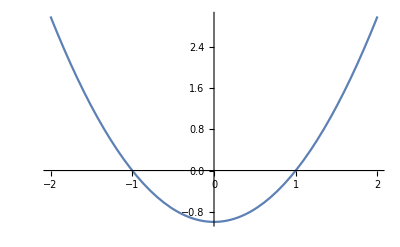

```mathematica
Plot[x^2-1,{x,-2,2}]
```

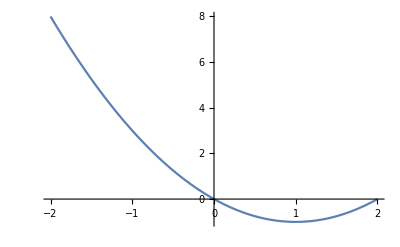

```mathematica
Plot[(x-1)^2-1,{x,-2,2}]
```

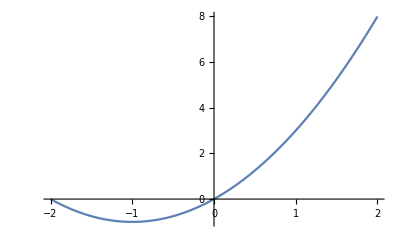

```mathematica
Plot[(x+1)^2-1,{x,-2,2}]
```

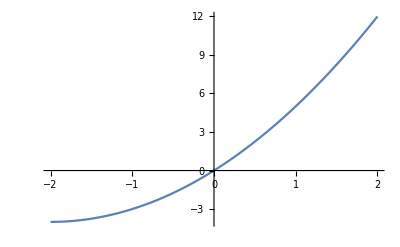

```mathematica
Plot[(x+2)^2-4,{x,-2,2}]
```

```mathematica
Manipulate[
Plot[(x+α)^2-α^2,{x,-5,5}]
,{α,0,2}]
```

```mathematica
Manipulate[
Plot[(x+α)^2-α^2,{x,-5,5},PlotRange->{-5,5}]
,{α,0,2}]
```

```mathematica
translateAlongCurve[x+α]==f[x+α]-f[α]
```

translateAlongCurve[x+α]==-f[α]+f[x+α]

```mathematica
translateAlongCurve[x+α]==f[x+α]-f[α]
```

translateAlongCurve[x+α]==-f[α]+f[x+α]

```mathematica
translateAlongCurve[x+α]==f[x+α]-f[α]==∫_α^(x+α) f'[t]ⅆt
```

translateAlongCurve[x+α]==-f[α]+f[x+α]==∫_α^(x+α) f'[t]ⅆt

```mathematica
Reduce[translateAlongCurve[x+α]==-f[α]+f[x+α]==∫_α^(x+α) f'[t]ⅆt]
```

∫_α^(x+α) f'[t]ⅆt==translateAlongCurve[x+α]&&f[α]==f[x+α]-translateAlongCurve[x+α]

```mathematica
With[{f=Function[x,x^3-x]},
Manipulate[
Plot[f[x+α]-f[α],{x,-2,2}]
,{{α,0},-5,5}]
]
```

```mathematica
With[{f=Function[x,x^3-x]},
Manipulate[
Plot[f[x+α]-f[α],{x,-2,2},PlotRange->{-3,3}]
,{{α,0},-5,5}]
]
```

```mathematica
With[{f=Function[x,x^3-x]},
Manipulate[
Plot[∫_α^(x+α) f'[t]ⅆt,{x,-2,2},PlotRange->{-3,3}]
,{{α,0},-5,5}]
]
```

```mathematica
With[{f=Function[x,x^3-x]},
D[f[x+α]-f[α],α]
]
```

-3 α^2+3 (x+α)^2

```mathematica
Simplify[-3 α^2+3 (x+α)^2]
```

3 x (x+2 α)

```mathematica
Manipulate[Plot[3 x (x+2 α),{x,-0.25424951236341525,0.25424951236341525}],{α,-0.28703703703703703,0.28703703703703703}]
```

```mathematica
1+x
```

1+x

```mathematica
With[{f=Function[x,x^3-x]},
Manipulate[
ParametricPlot[
{x,f[x+α]-f[α]}.RotationMatrix[θ]
,{x,-2,2},PlotRange->{-3,3}]
,{{α,0},-5,5},{θ,0,2π}]
]
```

```mathematica
{1,0}.Normalize@{1,1}
```

1/(√2)

```mathematica
N[1/(√2)]
```

0.707107

```mathematica
Normalize[{a,b}]=={a,b}/Norm[{a,b}]
```

True

```mathematica
Normalize[{a,b}].Normalize[{c,d}]==({a,b}/Norm[{a,b}]).({c,d}/Norm[{c,d}])
```

True

```mathematica
f==Normalize[{a,b}].Normalize[{c,d}]==({a,b}/Norm[{a,b}]).({c,d}/Norm[{c,d}])
```

f==(a c)/(√(Abs[a]^2+Abs[b]^2) √(Abs[c]^2+Abs[d]^2))+(b d)/(√(Abs[a]^2+Abs[b]^2) √(Abs[c]^2+Abs[d]^2))==(a c)/(√(Abs[a]^2+Abs[b]^2) √(Abs[c]^2+Abs[d]^2))+(b d)/(√(Abs[a]^2+Abs[b]^2) √(Abs[c]^2+Abs[d]^2))

```mathematica
Normalize[{a,b}].Normalize[{c,d}]==({a,b}/Norm[{a,b}]).({c,d}/Norm[{c,d}])
```

True

```mathematica
FullSimplify[f==Normalize[{a,b}].Normalize[{c,d}]==({a,b}/Norm[{a,b}]).({c,d}/Norm[{c,d}]),{a,b,c,d,f}∈Reals]
```

(a c+b d)/(√((a^2+b^2) (c^2+d^2)))==f

```mathematica
FullSimplify[f==Normalize[{a,b}].Normalize[{c,d}]==({a,b}/Norm[{a,b}]).({c,d}/Norm[{c,d}]),{a,b,c,d,f}∈Reals∧-1≤f≤1]
```

(a c+b d)/(√((a^2+b^2) (c^2+d^2)))==f

```mathematica
(a c+b d)/(√((a^2+b^2) (c^2+d^2)))==f
```

(a c+b d)/(√((a^2+b^2) (c^2+d^2)))==f

```mathematica
(a c+b d)/(√((a^2+b^2) (c^2+d^2)))==f/.{f->1,a->1,b->0}
```

c/(√(c^2+d^2))==1

```mathematica
FindInstance[c/(√(c^2+d^2))==1,{c,d}]
```

{{c→171/10-(103 ⅈ)/5,d→0}}

```mathematica
(a c+b d)/(√((a^2+b^2) (c^2+d^2)))==f/.{f->1,a->1,b->0}
```

```mathematica
(a c+b d)/(√((a^2+b^2) (c^2+d^2)))==f/.{f->1,a->1,b->0}
```

c/(√(c^2+d^2))==1

```mathematica
Solve[{c/(√(c^2+d^2))==1,√(c^2+d^2)==1},{c,d}]
```

{{c→1,d→0}}

```mathematica
(a c+b d)/(√((a^2+b^2) (c^2+d^2)))==f/.{f->0,a->1,b->0}
```

c/(√(c^2+d^2))==0

```mathematica
Solve[{c/(√(c^2+d^2))==0,√(c^2+d^2)==1},{c,d}]
```

{{c→0,d→-1},{c→0,d→1}}

```mathematica
(a c+b d)/(√((a^2+b^2) (c^2+d^2)))==f/.{f->1/2,a->1,b->0}
```

c/(√(c^2+d^2))==1/2

```mathematica
Solve[{c/(√(c^2+d^2))==1/2,√(c^2+d^2)==1},{c,d}]
```

{{c→1/2,d→-(√3)/2},{c→1/2,d→(√3)/2}}

```mathematica
Solve[{c/(√(c^2+d^2))==√2,√(c^2+d^2)==1},{c,d}]
```

{{c→√2,d→-ⅈ},{c→√2,d→ⅈ}}

```mathematica
Solve[{c/(√(c^2+d^2))==√2-1,√(c^2+d^2)==1},{c,d}]
```

{{c→√(3-2 √2),d→-√(2 (-1+√2))},{c→√(3-2 √2),d→√(2 (-1+√2))}}

```mathematica
2±1
```

2±1

```mathematica
Around[2,1]
```

2.01.0

```mathematica
2±1==Around[2,1]
```

2±1==2.01.0

```mathematica
ArcTan[2/1]
```

ArcTan[2]

```mathematica
N@ArcTan[2/4]
```

0.463648

```mathematica
ArcTan[x]
```

ArcTan[x]

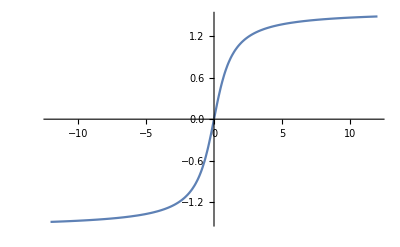

```mathematica
Plot[ArcTan[x],{x,-12.,12.}]
```

```mathematica
Manipulate[
Plot[ArcTan[x+α]-ArcTan[α],{x,-12.,12.}]
,{α,-4,4}]
```

```mathematica
Norm@{1,0}.Norm@{0,1}
```

1.1

```mathematica
Norm@{1,0} Norm@{0,1}
```

1

```mathematica
ArcTan[0]
```

0